```mathematica
(*
ForkNet   
Copyrights (c) Essam Rashed (essam.rashed@nitech.ac.jp), NITech, Nagoya, JP 
For any questions, please cnotact using the above e-mail address or (essam.rashed@gmial.com)
This code aims at mapping MRI 2D image with segmented labels of different anatomical structure. 
The design of ForkNet is based on unified encoders and individual decoders.
This implementation is for ForkNet (N=2) to segment MRI images of GM & WM. 
It is aimed to be a platform for further extensions and improvements.
This code is compatable with Mathematica 11.3 and byond and tested over Windows 10 and Ubuntu 16.04
More details are in our paper mentioned below. If you are using this code, please refer to our paper.

MRI data is available here: http://hdl.handle.net/1926/1687

→ Input images are in MATLAB "*.mat" formats for easy use 
→ To Run Select Evaluation → Evaluate Notebook 
Input: 256x256 (2D) MRI slices 
Outputs: 256x256 (2D) Label slices 

Reference:
Rashed, Gomez-Tames & Hirata, 
"Development of Accurate Human Head Model for Personalized Dosimetry Using Deep Learning", 2019 
(submitted for publication)
*)
```

```mathematica
(* Experiment Parameters ---------------------------------------------------------------*)
```

```mathematica
NIter=100; (* Training Iterations *)
```

```mathematica
BS=4; (* Batch Size *)
```

```mathematica
Dir="axial"; (* Slicing direction (axial/sagittal/coronal*)
```

```mathematica
TrainingPercentage=0.9; (* % of data used for training - remaining are for validation*)
```

```mathematica
(*----------------------LOAD DATA & Preprocessing-----------------------------------*)
```

```mathematica
NetworkName="/home/essam/Github/ForkNet/Results/ForkNet_"<>Dir<>"_"<>ToString[NIter]<>"_"<>ToString[BS]<>".wlnet";Print[Style["NetworkName >>> "<>NetworkName,Red]];
```

NetworkName >>> /home/essam/Github/ForkNet/Results/ForkNet_axial_100_4.wlnet

```mathematica
NetworkArch="/home/essam/Github/ForkNet/Arch/ForkNet_N_2.nb";Print[Style["NetworkArch >>> "<>NetworkArch,Red]];
```

NetworkArch >>> /home/essam/Github/ForkNet/Arch/ForkNet_N_2.nb

```mathematica
TestName="/home/essam/Github/ForkNet/Test/ForkNet_Test.nb";
```

```mathematica
LossName="/home/essam/Github/ForkNet/Results/ForkNet_Loss_"<>Dir<>"_"<>ToString[NIter]<>"_"<>ToString[BS]<>".txt";
```

```mathematica
VLossName="/home/essam/Github/ForkNet/Results/ForkNet_VLoss_"<>Dir<>"_"<>ToString[NIter]<>"_"<>ToString[BS]<>".txt";
```

```mathematica
(* Lodaind data... *)
```

```mathematica
(* This is just a sample data of single MRI image... Add more data for effective training *)
```

```mathematica
ana =Flatten[Import["/home/essam/Github/ForkNet/NAMIC/case01015.mat"],1]; (* anatomical volume *)
```

```mathematica
msk1 =Flatten[Import["/home/essam/Github/ForkNet/NAMIC/case01015_WM.mat"],1];  (* labels "1" *)
```

```mathematica
msk2 =Flatten[Import["/home/essam/Github/ForkNet/NAMIC/case01015_GM.mat"],1];   (* labels "2" *)
```

```mathematica
msk=Flatten[{msk1,msk2},1];
```

```mathematica
{a,b,c}=Dimensions[ana];
```

```mathematica
(*----------------------Preparing Data for ForkNet--------------------------------*)
```

```mathematica
images=Image3DSlices[Image3D[ana]];Clear[ana]
```

```mathematica
(* Shuffling... *)
```

```mathematica
miximages=RandomSample@Thread[Range@Length@images->images];
```

```mathematica
mixkeys=Keys@miximages;
```

```mathematica
mixmasks1=Lookup[<|Thread[Range@Length@msk1->msk1]|>,mixkeys];
```

```mathematica
mixmasks2=Lookup[<|Thread[Range@Length@msk2->msk2]|>,mixkeys];
```

```mathematica
(* Splitting... *)
```

```mathematica
TrainPack=Round[TrainingPercentage*a];ValPack=Round[(a-TrainPack)];
```

```mathematica
{MRId,MRIv}=TakeList[Values@miximages,{TrainPack,ValPack}];
```

```mathematica
{mskd1,mskv1}=TakeList[mixmasks1,{TrainPack,ValPack}];
```

```mathematica
{mskd2,mskv2}=TakeList[mixmasks2,{TrainPack,ValPack}];
```

```mathematica
(* prepare for ForkNet... *)
```

```mathematica
labels1d=ArrayReshape[mskd1,{TrainPack,1,b,c}];
```

```mathematica
labels2d=ArrayReshape[mskd2,{TrainPack,1,b,c}];
```

```mathematica
labels1v=ArrayReshape[mskv1,{ValPack,1,b,c}];
```

```mathematica
labels2v=ArrayReshape[mskv2,{ValPack,1,b,c}];
```

```mathematica
(* load ForkNet architecture *)
```

```mathematica
NotebookEvaluate[NetworkArch];  ForkNET
```

NetGraph[<>]

```mathematica
(* Training...*)
```

```mathematica
logFile=CreateTemporary[]; (* save training data into TMP file *)appendToLog=PutAppend[<|"Batch"->#AbsoluteBatch,"Loss"->#RoundLoss,"VLoss"->#ValidationLoss(*, "Error"->#RoundErrorRate*)|>,logFile]&;TN=NetTrain[ForkNET,
<|"Input" ->MRId,"Output1"->labels1d,"Output2"->labels2d|>,
BatchSize->BS,
ValidationSet-> <|"Input" ->MRIv,"Output1"->labels1v,"Output2"->labels2v|>,
MaxTrainingRounds->NIter, 
TargetDevice->{"GPU",3}, (* "3" is the number of available GPU cards - remove this line if you do the computation on CPU*)
TrainingProgressFunction->appendToLog
 ];
```

```mathematica
(* Plot training loss and validation loss  *)
```

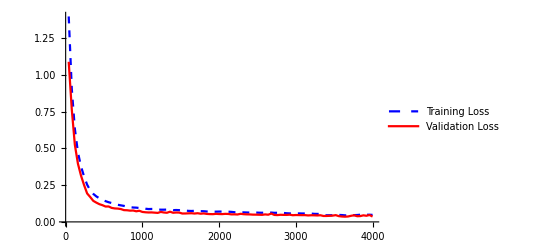

```mathematica
dataset=Dataset[ReadList[logFile]];
LossData=dataset[All,{"Batch","Loss"}];VLossData=dataset[All,{"Batch","VLoss"}];
t1=ListLinePlot[LossData,PlotRange->All,PlotLegends->{"Training Loss"},PlotStyle->{Dashed, Blue}];t2=ListLinePlot[VLossData,PlotRange->All,PlotLegends->{"Validation Loss"},PlotStyle->{Red}];Show[t1,t2]
```

```mathematica
(* Save trained network & loss data *)
```

```mathematica
Export[NetworkName,TN];
```

```mathematica
Export[LossName,LossData,"Table"];
```

```mathematica
Export[VLossName,VLossData,"Table"];
```

```mathematica
(* Test one random image from the validation data ("Yellow" is true and "Green" is network segmentation )*)
```

```mathematica
selectval=RandomInteger[Dimensions[MRIv]-1]+1;
```

```mathematica
NotebookEvaluate[TestName];DisplayResult
```

-Graphics-

```mathematica
(* WM (True)     -      WM (ForkNet)      -        GM (True)       -        GM (ForkNet) *)
```